```mathematica
f[x_,y_]:=Cos[x]+ Sin[y]
```

```mathematica
f[π,1.6]
```

-0.000426397

```mathematica
f[θ,ρ]
```

Cos[θ]+Sin[ρ]

```mathematica
Integrate[Exp[I π x],{x,a,b}]
```

(ⅈ (ⅇ^(ⅈ a π)-ⅇ^(ⅈ b π)))/π

```mathematica
Integrate[Exp[I π x],x]
```

-(ⅈ ⅇ^(ⅈ π x))/π

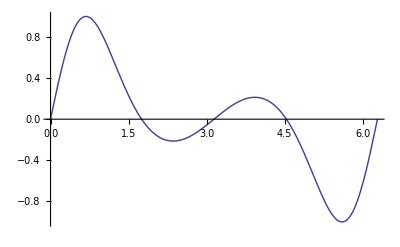

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,2π}]
```

```mathematica
lis={{α,1},{β,2},{γ,3}}
```

{{α,1},{β,2},{γ,3}}

```mathematica
temp=lis;
```

```mathematica
Do[{temp[[i,1]],temp[[i,2]]}={lis[[i,2]],lis[[i,1]]},{i,1,Length[lis]}];
```

```mathematica
temp
```

{{1,α},{2,β},{3,γ}}

```mathematica
Table[{lis[[i,2]],lis[[i,1]]},{i,1,3}]
```

{{1,α},{2,β},{3,γ}}

```mathematica
Map[Reverse,lis]
```

{{1,α},{2,β},{3,γ}}

```mathematica
Map[Head,{3,22/7,π}]
```

{Integer,Rational,Symbol}

```mathematica
Map[f,g[a,b,c]]
```

g[f[a],f[b],f[c]]

```mathematica
vec={2,π,γ};
f[x_]:=x^2+1
```

```mathematica
Map[f,vec]
```

{5,1+π^2,1+γ^2}

```mathematica
Thread[g[{a,b,c},{x,y,z}]]
```

{g[a,x],g[b,y],g[c,z]}

```mathematica
MapThread[g,{{a,b,c},{x,y,z}}]
```

{g[a,x],g[b,y],g[c,z]}

```mathematica
Thread[Equal[{a,b,c},{x,y,z}]]
```

{a==x,b==y,c==z}

```mathematica
Map[FullForm,%]
```

{Equal[a,x],Equal[b,y],Equal[c,z]}

```mathematica
values={x1,x2,x3,x4,x5};
vars={1.2,2.5,5.7,8.21,6.66};
Thread[Rule[vars,values]]
```

{1.2→x1,2.5→x2,5.7→x3,8.21→x4,6.66→x5}

```mathematica
??Rule
```

RowBox[{StyleBox["lhs", "TI"], "->", StyleBox["rhs", "TI"]}] or RowBox[{StyleBox["lhs", "TI"], "→", StyleBox["rhs", "TI"]}] represents a rule that transforms StyleBox["lhs", "TI"] to StyleBox["rhs", "TI"].

Attributes[Rule]={Protected,SequenceHold}

```mathematica
MapThread[Power,{{2,6,3},{5,1,2}}]//Trace
```

{MapThread[Power,{{2,6,3},{5,1,2}}],{2^5,6^1,3^2},{2^5,32},{6^1,6},{3^2,9},{32,6,9}}

```mathematica
MapThread[List,{{5,3,2},{6,4,9}}]//MatrixForm
```

(5 | 6
3 | 4
2 | 9)

```mathematica
Log[{a,E,1}]
```

{Log[a],1,0}

```mathematica
Map[Log,{a,E,1}]
```

{Log[a],1,0}

```mathematica
{4,6,3}+{5,1,2}
```

{9,7,5}

```mathematica
MapThread[Plus,{{4,6,3},{5,1,2}}]
```

{9,7,5}

```mathematica
Plus[{4,6,3},{5,1,2}]
```

{9,7,5}

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
g[{{a,b},{c,d}}]
```

g[{{a,b},{c,d}}]

```mathematica
SetAttributes[g,Listable]
```

```mathematica
g[{{a,b},{c,d}}]
```

{{g[a],g[b]},{g[c],g[d]}}

```mathematica
g[{a,b},{c,d}]
```

{g[a,c],g[b,d]}

```mathematica
Clear[g]
```

```mathematica
?g
```

Global`g

Attributes[g]={Listable}

```mathematica
ClearAll[g]
```

```mathematica
?g
```

Global`g

```mathematica
Remove[g]
```

```mathematica
?g
```

Information::notfound: Symbol "g" not found.

```mathematica
Apply[h,g[a,b,c]]
```

h[a,b,c]

```mathematica
Apply[h,{a,b,c}]
```

h[a,b,c]

```mathematica
Apply[h,List[a,b,c]]
```

h[a,b,c]

```mathematica
Apply[Plus,{1,2,3,4}]
```

10

```mathematica
Apply[Plus,{{1,2,3},{5,6,7}}]
```

{6,8,10}

```mathematica
Map[h,{{a,b},{c,d}},{2}]
```

{{h[a],h[b]},{h[c],h[d]}}

```mathematica
Apply[Plus,{{1,2,3},{5,6,7}},{1}]
```

{6,18}

```mathematica
Apply[h,{{1,2,3},{5,6,7}},{1}]
```

{h[1,2,3],h[5,6,7]}

```mathematica
ClearAll[f]
```

```mathematica
Outer[f,{a,b},{2,3,4}]
```

{{f[a,2],f[a,3],f[a,4]},{f[b,2],f[b,3],f[b,4]}}

```mathematica
?Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
Outer[List,{a,b},{2,3,4}]
```

{{{a,2},{a,3},{a,4}},{{b,2},{b,3},{b,4}}}

```mathematica
Inner[f,{a,b,c},{d,e,f},g]
```

g[f[a,d],f[b,e],f[c,f]]

```mathematica
?Inner
```

Inner[f,list_1,list_2,g] is a generalization of Dot in which f plays the role of multiplication and g of addition.

```mathematica
Inner[Times,{x1,y1,z1},{x2,y2,z2},Plus]
```

x1 x2+y1 y2+z1 z2

```mathematica
Inner[List,{a,b,c},{d,e,f},Plus]
```

{a+b+c,d+e+f}

```mathematica
data={{ 1,2},{2,3},{3,4},{4,5},{5,6}};
```

```mathematica
Apply[Plus,data,{1}]
```

{3,5,7,9,11}

```mathematica
Map[Reverse,Transpose[{{1,2,3},{4,5,6}}]]
```

{{4,1},{5,2},{6,3}}

```mathematica
Apply[Plus,MapThread[Times,{Transpose[{{1,2},{3,4}}],{x,y}}]]
```

{x+2 y,3 x+4 y}

```mathematica
FactorInteger[3628800]
```

{{2,8},{3,4},{5,2},{7,1}}

```mathematica
Inner[Power,Transpose[{{2,8},{3,4},{5,2},{7,1}}][[1]],Transpose[{{2,8},{3,4},{5,2},{7,1}}][[2]],Times]
```

3628800

```mathematica
div[vecs_,vars_]:=Inner[D,vecs,vars,Plus]
```

```mathematica
div[{e1[v1,v2,v3],e2[v1,v2,v3],e3[v1,v2,v3]},{v1,v2,v3}]
```

e3^(0,0,1)[v1,v2,v3]+e2^(0,1,0)[v1,v2,v3]+e1^(1,0,0)[v1,v2,v3]

```mathematica
Nest[g,a,4]
```

g[g[g[g[a]]]]

```mathematica
NestList[g,a,4]
```

{a,g[a],g[g[a]],g[g[g[a]]],g[g[g[g[a]]]]}

```mathematica
NestList[Cos,0.85,10]
```

{0.85,0.659983,0.790003,0.703843,0.76236,0.723208,0.749687,0.731902,0.743904,0.73583,0.741274}

```mathematica
FixedPoint[Cos,0.85]
```

0.739085

```mathematica
FixedPoint[Cos,0.5]
```

0.739085

```mathematica
Fold[f,x,{a,b,c}]
```

f[f[f[x,a],b],c]

```mathematica
FoldList[f,x,{a,b,c}]
```

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c]}

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

{0,a,a+b,a+b+c,a+b+c+d}

```mathematica
fac[n_]:=Fold[Times,1,Array[Identity,n]]
```

```mathematica
fac[5]
```

120

```mathematica
fac[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
maxima[lis_]:=Union[Rest[FoldList[Max,0,lis]]]
```

```mathematica
maxima[{4,2,7,3,4,9,14,11,17}]
```

{4,7,9,14,17}

```mathematica
cardDeck=Flatten[
Outer[List,{♣,♢,♡,♠},Join[Range[2,10],{J,Q,K,A}]],1]
```

{{♣,2},{♣,3},{♣,4},{♣,5},{♣,6},{♣,7},{♣,8},{♣,9},{♣,10},{♣,J},{♣,Q},{♣,K},{♣,A},{♢,2},{♢,3},{♢,4},{♢,5},{♢,6},{♢,7},{♢,8},{♢,9},{♢,10},{♢,J},{♢,Q},{♢,K},{♢,A},{♡,2},{♡,3},{♡,4},{♡,5},{♡,6},{♡,7},{♡,8},{♡,9},{♡,10},{♡,J},{♡,Q},{♡,K},{♡,A},{♠,2},{♠,3},{♠,4},{♠,5},{♠,6},{♠,7},{♠,8},{♠,9},{♠,10},{♠,J},{♠,Q},{♠,K},{♠,A}}

```mathematica
?Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

```mathematica
removeRand[lis_]:=Delete[lis,Random[Integer,{1,Length[lis]}]]
```

```mathematica
lis=Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
removeRand[lis]
```

{1,2,3,4,5,6,7,9,10}

```mathematica
deal[n_]:=Complement[cardDeck,Nest[removeRand,cardDeck,n]]
```

```mathematica
deal[5]
```

{{♣,K},{♣,Q},{♢,6},{♢,9},{♠,7}}

```mathematica
cardDeck//Length
```

52

```mathematica
pick[n_]:=Table[Random[Integer,{0,9}],{n}]
```

```mathematica
pick[5]
```

{8,7,1,2,4}

```mathematica
chooseWithReplacement[lis_,n_]:=
Table[Part[lis,Random[Integer,{0,n}]],{n}]
```

```mathematica
chooseWithReplacement[Range[0,10],5]
```

{4,2,4,1,0}

```mathematica
{3,4}^2
```

{9,16}

```mathematica
distance[a_,b_]:=Sqrt[Apply[Plus,(a-b)^2]]
```

```mathematica
distance[{1,2},{4,6}]
```

5

```mathematica
Block[{$RecursionLimit=20},
x=g[x]]
```

$RecursionLimit::reclim: Recursion depth of 20 exceeded.

g[g[g[g[g[g[g[g[g[g[g[g[g[g[g[g[g[g[Hold[g[x]]]]]]]]]]]]]]]]]]]]

```mathematica
$RecursionLimit
```

256

```mathematica
y=5
```

5

```mathematica
f[x_]:=With[{y=x+1},y]
```

```mathematica
f[2]
```

3

```mathematica
?f
```

Global`f

f[x_]:=With[{y=x+1},y]

```mathematica
With[{y=y},g[x_]:=x*y]
```

```mathematica
g[2]
```

10

```mathematica
?g
```

Global`g

g[x$_]:=x$ 5

```mathematica
y
```

5

```mathematica
y=1
```

1

```mathematica
g[2]
```

10

```mathematica
Function[z,z^2][6]
```

36

```mathematica
(#^2&)[6]
```

36

```mathematica
squared=(#^2)&;
squared[6]
```

36

```mathematica
lis={2,-5,6.1}
```

{2,-5,6.1}

```mathematica
Map[#^2+1&,lis]
```

{5,26,38.21}

```mathematica
data={24.39001,29.669,9.321,20.8856,23.4736,22.1488,24.7434,22.1619,21.1039,24.8177,27.1331,25.8705,39.7676,24.7762}
```

{24.39,29.669,9.321,20.8856,23.4736,22.1488,24.7434,22.1619,21.1039,24.8177,27.1331,25.8705,39.7676,24.7762}

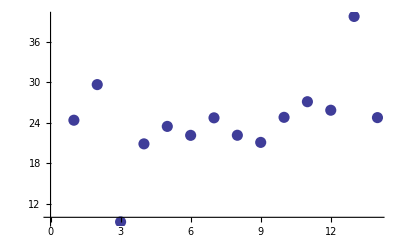

```mathematica
ListPlot[data,PlotStyle->PointSize[.02]]
```

```mathematica
Select[data,20≤#≤30&]
```

{24.39,29.669,20.8856,23.4736,22.1488,24.7434,22.1619,21.1039,24.8177,27.1331,25.8705,24.7762}

```mathematica
areEltsEven[lis_]:=Apply[And,Map[EvenQ,lis]]
```

```mathematica
areEltsEven[{2,4,5,8}]
```

False

```mathematica
(Apply[And,Map[EvenQ,#1]])&[{2,4,5,8}]
```

False

```mathematica
maxima=Function[x,Union[Rest[FoldList[Max,0,x]]]]
```

Function[x,Union[Rest[FoldList[Max,0,x]]]]

```mathematica
maxima[{2,6,3,7,9,2}]
```

{2,6,7,9}

```mathematica
Map[#^2&,{3,2,7}]
```

{9,4,49}

```mathematica
Function[y,Map[Function[x,x^2],y]][{3,2,7}]
```

{9,4,49}

```mathematica
sumSquare=Function[lis,Fold[Plus,0,lis^2]]
```

Function[lis,Fold[Plus,0,lis^2]]

```mathematica
sumSquare[{1,2,3,4}]
```

30

```mathematica
?IntegerDigits
```

IntegerDigits[n] gives a list of the decimal digits in the integer n. 
IntegerDigits[n,b] gives a list of the base-b digits in the integer n. 
IntegerDigits[n,b,len] pads the list on the left with zeros to give a list of length len.

```mathematica
?Distribute
```

Distribute[f[x_1,x_2,…]] distributes f over Plus appearing in any of the x_i. 
Distribute[expr,g] distributes over g. 
Distribute[expr,g,f] performs the distribution only if the head of expr is f.

```mathematica
pts={p1,p2,p3};
Distribute[{pts,pts},List]
```

{{p1,p1},{p1,p2},{p1,p3},{p2,p1},{p2,p2},{p2,p3},{p3,p1},{p3,p2},{p3,p3}}

```mathematica
?Permutations
```

Permutations[list] generates a list of all possible permutations of the elements in list. 
Permutations[list,n] gives all permutations containing at most n elements.
Permutations[list,{n}] gives all permutations containing exactly n elements.

```mathematica
Permutations[pts]
```

{{p1,p2,p3},{p1,p3,p2},{p2,p1,p3},{p2,p3,p1},{p3,p1,p2},{p3,p2,p1}}

```mathematica
Permutations[pts,2]
```

{{},{p1},{p2},{p3},{p1,p2},{p1,p3},{p2,p1},{p2,p3},{p3,p1},{p3,p2}}

```mathematica
Permutations[pts,{2}]
```

{{p1,p2},{p1,p3},{p2,p1},{p2,p3},{p3,p1},{p3,p2}}

```mathematica
removeRand=Delete[#,Random[Integer,{1,Length[#]}]]&
```

Delete[#1,Random[Integer,{1,Length[#1]}]]&

```mathematica
removeRand[{1,2,3,4,5}]
```

{2,3,4,5}

```mathematica
removeRand[{1,2,3,4,5}]
```

{1,2,3,4}

```mathematica
?Repeated
```

p.. or Repeated[p] is a pattern object which represents a sequence of one or more expressions, each matching p. 
Repeated[p,max] represents up to max expressions matching p.
Repeated[p,{min,max}] represents between min and max expressions matching p.
Repeated[p,{n}] represents exactly n expressions matching p.

```mathematica
repUnit[n_]:=Table[1,{n}]
```

```mathematica
repUnit[10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
ClearAll[x,y,f,g]
```

```mathematica
Horner[lis_,var_]:=Fold[Function[{acc,next},acc var+next],0,lis]
```

```mathematica
Horner[{a,b,c,d},x]
```

d+x (c+x (b+a x))

```mathematica
Expand[%]
```

d+c x+b x^2+a x^3

```mathematica
hammingDistance[lis1_,lis2_]:=
Count[MapThread[SameQ,{lis1,lis2}],False]
```

```mathematica
hammingDistance[{1,0,0,1,1},{0,1,0,1,0}]
```

3

```mathematica
hammingDistance2[lis1_,lis2_]:=
Apply[Plus,Apply[BitXor,Transpose[{lis1,lis2}],{1}]]
```

```mathematica
hammingDistance2[{1,0,0,1,1},{0,1,0,1,0}]
```

3

```mathematica
data1=Table[Random[Integer],{10^6}];
data2=Table[Random[Integer],{10^6}];
Timing[hammingDistance[data1,data2]]
```

{0.999952,500029}

```mathematica
Timing[hammingDistance2[data1,data2]]
```

{1.45003,500029}

```mathematica
Timing[HammingDistance[data1,data2]]
```

{0.218001,500029}

```mathematica
Rest[RotateLeft[#]]&[{a,b,c,d}]
```

{c,d,a}

```mathematica
survivor[lis_]:=
Nest[Rest[RotateLeft[#]]&,lis,Length[lis]-1]
```

```mathematica
survivor[Range[10]]
```

{5}

```mathematica
TracePrint[survivor[Range[6]],RotateLeft]
```

RotateLeft

{2,3,4,5,6,1}

RotateLeft

{4,5,6,1,3}

RotateLeft

{6,1,3,5}

RotateLeft

{3,5,1}

RotateLeft

{1,5}

{5}

```mathematica
Table[survivor[Range[i]],{i,1,100}]
```

{{1},{1},{3},{1},{3},{5},{7},{1},{3},{5},{7},{9},{11},{13},{15},{1},{3},{5},{7},{9},{11},{13},{15},{17},{19},{21},{23},{25},{27},{29},{31},{1},{3},{5},{7},{9},{11},{13},{15},{17},{19},{21},{23},{25},{27},{29},{31},{33},{35},{37},{39},{41},{43},{45},{47},{49},{51},{53},{55},{57},{59},{61},{63},{1},{3},{5},{7},{9},{11},{13},{15},{17},{19},{21},{23},{25},{27},{29},{31},{33},{35},{37},{39},{41},{43},{45},{47},{49},{51},{53},{55},{57},{59},{61},{63},{65},{67},{69},{71},{73}}

```mathematica
coins={p,p,q,n,d,d,p,q,q,p}
```

{p,p,q,n,d,d,p,q,q,p}

```mathematica
Count[coins,p]
```

4

```mathematica
{Count[coins,p],Count[coins,n],
Count[coins,d],Count[coins,q]}
```

{4,1,2,3}

```mathematica
Map[Count[coins,#]&,{p,n,d,q}]
```

{4,1,2,3}

```mathematica
Dot[{4,1,2,3},{1,5,10,25}]
```

104

```mathematica
pocketChange[x_]:=
Map[Count[x,#]&,{p,n,d,q}].{1,5,10,25}
```

```mathematica
pocketChange[coins]
```

104

```mathematica
frequencies[lis_]:=Map[({#,Count[lis,#]})&,Union[lis]]
```

```mathematica
frequencies[{a,a,b,b,b,a,c,c}]
```

{{a,3},{b,3},{c,2}}

```mathematica
Union[{a,a,b,b,b,a,c,c}]
```

{a,b,c}

```mathematica
split[lis_,parts_]:=
(Inner[Take[lis,{#1,#2}]&,Drop[#1,-1]+1,
Rest[#1],List]&)[FoldList[Plus,0,parts]]
```

```mathematica
split[Range[10],{2,5,0,3}]
```

{{1,2},{3,4,5,6,7},{},{8,9,10}}

```mathematica
split2[lis_,parts_]:=
Map[(Take[lis,#+{1,0}])&,
Partition[FoldList[Plus,0,parts],2,1]]
```

```mathematica
split2[Range[10],{2,5,0,3}]
```

{{1,2},{3,4,5,6,7},{},{8,9,10}}

```mathematica
FoldList[Mod,119,{25,10,5}]
```

{119,19,9,4}

```mathematica
makeChange[d_]:=Quotient[FoldList[Mod, d,{25,10,5}],{25,10,5,1}]
```

```mathematica
makeChange[119]
```

{4,1,1,4}

```mathematica
randomWalk2D[steps_]:=
Map[({Sin[#],Cos[#]})&,RandomReal[{0,2π},steps]]
```

```mathematica
randomWalk2D[10]
```

{{0.994187,-0.107667},{0.740018,0.672587},{-0.58072,-0.814104},{-0.999881,0.0154466},{0.0580985,-0.998311},{0.996063,-0.0886452},{0.518882,-0.854846},{0.729537,-0.683941},{-0.677285,0.735721},{-0.080852,0.996726}}